```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
```

```mathematica
CfgDecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
tcorrs=Table[{(j-t)*dt,
Cos[anglesT[[j,i]]-anglesT[[t,i]]]},
{t,1,Length[rt],100},(*Length[rt]},*)
{j,t,Length[rt]},
{i,Length[rt[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
DecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
anglesBwT = Table[anglesT[[t,i+1]] -anglesT[[t,i]],
{t,1,Length[anglesT]},
{i,1,Length[anglesT[[t]]]-1}];
tcorrs=Table[{(j-t)*dt,
Cos[(anglesBwT[[j,i]]-anglesBwT[[t,i]])*12]},
{t,1,Length[anglesBwT],10},
{j,t,Length[anglesBwT],10},
{i,Length[anglesBwT[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
CCF[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
ld=Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
corrs=Table[{(j-i)*ld,
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,Length[rt[[t]]]},
{j,i,Length[rt[[t]]]}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
{ccf,errs}
];
```

```mathematica
seeds=Table[ToString[i],{i,1200,1247}];
basedir="nmon50_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfs=Table[CCF[dr,1],{dr,dirs}];
```

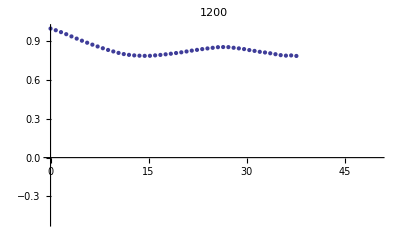
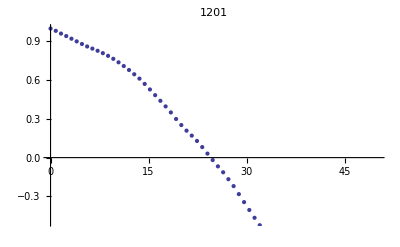
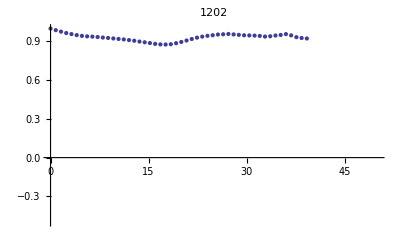
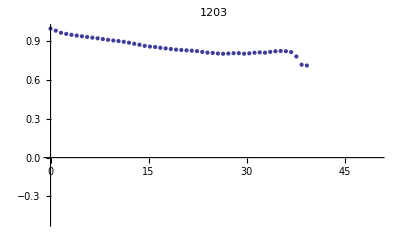
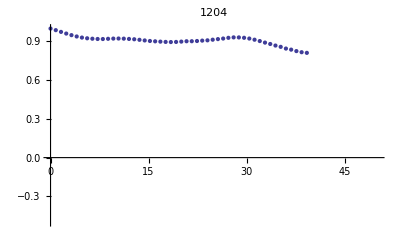
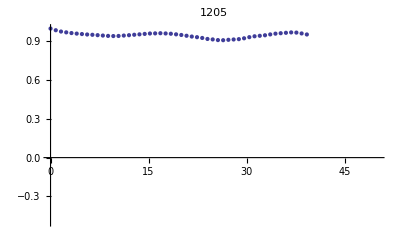
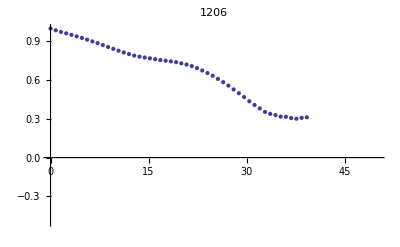
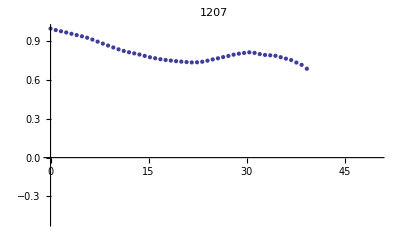

```mathematica
Table[ListPlot[ccfs[[i,1]],PlotLabel->seeds[[i]],PlotRange->{{0,50},{-0.5,1}}],{i,Length[ccfs]}]
```

```mathematica
nlms=Table[
NonlinearModelFit[
ccfs[[i,1,2;;]],
Exp[-x/(2Lp)],
{Lp},
x,
Weights->1/ccfs[[i,2,2;;]]^2
],
{i,Length[ccfs]}];
```

```mathematica
Table[{nlms[[i]]["ParameterTable"],seeds[[i]]},{i,Length[nlms]}]//TableForm
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 47.9571 | 3.70089 | 12.9583 | 5.83625×10^-17 | 1200
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 10.0448 | 1.1049 | 9.09114 | 5.20992×10^-12 | 1201
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 159.39 | 19.9873 | 7.97459 | 2.40571×10^-10 | 1202
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 55.0515 | 1.48886 | 36.9756 | 6.25775×10^-37 | 1203
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 98.5462 | 8.22948 | 11.9748 | 5.03877×10^-16 | 1204
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 198.204 | 18.2949 | 10.8338 | 1.72467×10^-14 | 1205
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 26.344 | 0.851218 | 30.9486 | 2.2834×10^-33 | 1206
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 40.6662 | 1.83919 | 22.111 | 8.14716×10^-27 | 1207
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 147.504 | 16.4218 | 8.98219 | 7.53266×10^-12 | 1208
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 76.0875 | 3.47479 | 21.897 | 1.24676×10^-26 | 1209
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 69.8855 | 3.75735 | 18.5997 | 1.39747×10^-23 | 1210
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 44.217 | 2.26917 | 19.4859 | 1.93297×10^-24 | 1211
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 22.3089 | 1.08928 | 20.4803 | 4.60423×10^-25 | 1212
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 57.4454 | 6.06023 | 9.47908 | 1.41671×10^-12 | 1213
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 31.3251 | 1.44597 | 21.6637 | 1.99039×10^-26 | 1214
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 60.7849 | 5.08418 | 11.9557 | 1.45012×10^-15 | 1215
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 9.56442 | 1.49735 | 6.38758 | 1.21563×10^-7 | 1216
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 58.4989 | 5.50641 | 10.6238 | 3.36597×10^-14 | 1217
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 45.5382 | 1.11367 | 40.8901 | 5.78159×10^-39 | 1218
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 55.8091 | 4.17022 | 13.3828 | 6.2511×10^-17 | 1219
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 36.2225 | 2.36081 | 15.3433 | 3.88345×10^-20 | 1220
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 23.2213 | 0.372438 | 62.3494 | 1.35373×10^-47 | 1221
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 3617. | 730.172 | 4.95363 | 9.43918×10^-6 | 1222
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 14.8369 | 0.896182 | 16.5557 | 1.78186×10^-21 | 1223
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 16.0017 | 1.28303 | 12.4719 | 7.05578×10^-16 | 1224
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 98.2492 | 5.57001 | 17.639 | 1.29583×10^-22 | 1225
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 84.9706 | 3.51117 | 24.2001 | 1.51685×10^-28 | 1226
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 7.93933 | 1.0124 | 7.84208 | 1.09576×10^-9 | 1227
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 133.067 | 12.0226 | 11.068 | 8.23823×10^-15 | 1228
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 24.9754 | 0.943061 | 26.4833 | 2.69124×10^-30 | 1229
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 35.0695 | 1.78902 | 19.6026 | 1.49751×10^-24 | 1230
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 11.2346 | 0.733082 | 15.3252 | 7.46409×10^-18 | 1231
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 39.9444 | 1.94216 | 20.567 | 3.84981×10^-25 | 1232
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 74.8073 | 4.82879 | 15.4919 | 2.63826×10^-20 | 1233
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 70.5065 | 5.47171 | 12.8857 | 3.3855×10^-17 | 1234
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 164.393 | 14.3902 | 11.4239 | 2.71655×10^-15 | 1235
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 39.4403 | 1.46753 | 26.8754 | 1.3887×10^-30 | 1236
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 92.5027 | 5.79655 | 15.9582 | 7.97288×10^-21 | 1237
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 88.4851 | 7.21734 | 12.2601 | 6.06844×10^-16 | 1238
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 81.0419 | 12.2385 | 6.62189 | 2.79589×10^-8 | 1239
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 122.727 | 10.7046 | 11.465 | 8.35955×10^-15 | 1240
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 138.299 | 19.7024 | 7.0194 | 6.86654×10^-9 | 1241
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 32.8628 | 1.52831 | 21.5027 | 2.75564×10^-26 | 1242
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 56.9756 | 3.42016 | 16.6587 | 1.38154×10^-21 | 1243
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 39.6463 | 2.9503 | 13.4381 | 6.9307×10^-18 | 1244
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 166.715 | 22.8224 | 7.30489 | 2.51027×10^-9 | 1245
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 24.0843 | 0.745263 | 32.3165 | 3.14365×10^-34 | 1246
 | Estimate | Standard Error | t-Statistic | P-Value
Lp | 8.32159 | 1.03678 | 8.02637 | 4.3501×10^-10 | 1247

```mathematica
nlms[[23]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 3617. | 730.172 | 4.95363 | 9.43918×10^-6

```mathematica
nlms=Delete[nlms,23];
```

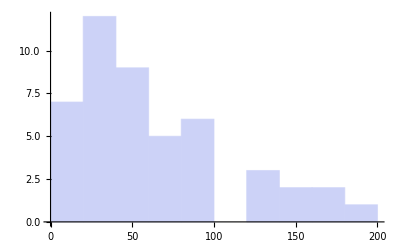

```mathematica
Histogram[Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}],10]
```

```mathematica
pls=Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}];
```

```mathematica
Mean[pls]
```

64.7173

```mathematica
Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]
```

40

```mathematica
meanccfs=Total[ccfs[[All,1,1;;Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]]]]/Length[ccfs];
```

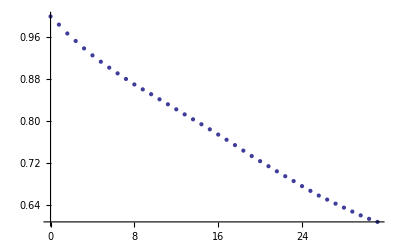

```mathematica
ListPlot[meanccfs]
```

```mathematica
nlm=NonlinearModelFit[
meanccfs,
Exp[-x/(2Lp)],
{Lp},
x];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 30.7481 | 0.123067 | 249.849 | 4.11909×10^-64